```mathematica
Quit[]
```

### linear slope

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

dxL+dotxL/(3 H)-(dotxL ⅇ^(3 H (-t+tL)))/(3 H)+xL+(F0 (1-3 H t+3 H tL-(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]))/(9 H^2)

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+ϵ xi0]==xSR[t]/.{dxL->ϵ dxL}]/.{tc->tcUSR}]
```

1/(9 H^2)(3 dotxL ⅇ^(3 H (-t+tL)) H-3 dotxL ⅇ^(-3 H (t-tL+xi0 ϵ)) H+(dotxL ⅇ^(3 H (-t+tL)) F0)/(dotxL-3 H xc+3 H xL)+9 dxL H^2 ϵ-3 F0 H xi0 ϵ-(dotxL ⅇ^(-3 H (t-tL+xi0 ϵ)) F0)/(dotxL+3 H (-xc+xL+dxL ϵ))-F0 Log[dotxL/(dotxL+3 H (-xc+xL))]+F0 Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))])==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{ϵ,0,1}]]/.{ϵ->1}//Simplify
```

dxL+dotxL ⅇ^(3 H (-t+tL)) xi0+(dotxL ⅇ^(3 H (-t+tL)) F0 (dxL+xi0 (dotxL+3 H (-xc+xL))))/(3 H (dotxL+3 H (-xc+xL))^2)==(F0 (xi0+dxL/(dotxL+3 H (-xc+xL))))/(3 H)

```mathematica
xi0SR[t_]=xi0/.Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

(dxL (-dotxc F0+dotxL ⅇ^(3 H (-t+tL)) F0+3 dotxc^2 H))/(dotxc (-dotxL ⅇ^(3 H (-t+tL)) F0+dotxc (F0-3 dotxL ⅇ^(3 H (-t+tL)) H)))

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(dxL ⅇ^(3 H (-t+tc)) F0)/dotxc

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

-(dotxL ⅇ^(3 H (-t+tL)) F0)/dotxc^2

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

-(3 dotxc^2 ⅇ^(3 H (t-tL)) H)/(dotxL F0)

bispectrum correction reads

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->-dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-6 Ps zetaL

### quadratic slope

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tc)+3 H (-tc+tL)) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))))/(√(9 H^2+4 m^2))+xc

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc-1/(√(9 H^2+4 m^2))ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL-Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H))) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)))) (dotxL+3 H (dxL-xc+xL))

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+ϵ xi0]==xSR[t]/.{dxL->ϵ dxL}]/.{tc->tcUSR}]
```

1/(√(9 H^2+4 m^2))(ⅇ^(-1/2 (3 H+√(9 H^2+4 m^2)) (t-tL)) (dotxL-dotxL ⅇ^(√(9 H^2+4 m^2) (t-tL-Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) (dotxL/(dotxL-3 H xc+3 H xL))^(1/6 (-3+(√(9 H^2+4 m^2))/H))-ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL+xi0 ϵ-Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))]/(3 H))) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL-xi0 ϵ+Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))]/(3 H)))) (dotxL+3 H (-xc+xL+dxL ϵ)))==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{ϵ,0,1}]]/.{ϵ->1}//Simplify
```

1/(√(9 H^2+4 m^2))ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL-Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H))) (3 dxL (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) H-dxL (1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) √(9 H^2+4 m^2)+(3 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) H+(1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) √(9 H^2+4 m^2)) xi0 (-dotxL+3 H (xc-xL)))==0

```mathematica
xi0SR[t_]=Simplify[Simplify[Simplify[xi0/.Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxc->dotxL Exp[-3H(tc-tL)]},{H>0,tc-tL>0}]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{H->(-Cp-Cm)/3}//Simplify
```

(dxL (-Cm+Cp ⅇ^((Cm-Cp) (t-tc))))/(dotxc (-Cp+Cm ⅇ^((Cm-Cp) (t-tc))))

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=Simplify[Simplify[xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]/.{dotxc->dotxL Exp[-3H(tc-tL)]}/.{H->(-Cp-Cm)/3}]
```

(Cm Cp dxL (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))))/(Cm-Cp)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=Simplify[Simplify[D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}/.{dotxL->dotxc Exp[3H(tc-tL)]},{H>0,tc>tL}]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]
```

((ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)/(Cm-Cp)

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

(3 (Cm-Cp) H)/((ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)

zetaS can be understood as H xi0 with the replacement dxL→dxS

```mathematica
Limit[H xi0SR[t]/.{dxL->dxS},{t->∞},Assumptions->{Cp-Cm>0}]
```

(Cm dxS H)/(Cp dotxc)

Thus 𝒫_ζ_S=(C_-)^2/(C_+)^2 H^2/((ϕ̇)_c)^2(H/(2π))^2

bispectrum correction reads

```mathematica
ddotxcddxL/ddotxddxL(-2/dotxc Ps)
```

-(6 (Cm-Cp) H Ps)/(dotxc (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->Cp/Cm dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-(6 Cp^2 Ps zetaL)/m^2

```mathematica
Simplify[Normal[Series[(-3H+√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

m^2/(3 H)

### Suyama-san’s general formula

#### linear slope

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
Simplify[Solve[tc==tcUSR,xc],{tc>tL,H>0}][[1]]
```

{xc→(dotxL-dotxL ⅇ^(3 H (-tc+tL))+3 H xL)/(3 H)}

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

dxL+dotxL/(3 H)-(dotxL ⅇ^(3 H (-t+tL)))/(3 H)+xL+(F0 (1-3 H t+3 H tL-(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]))/(9 H^2)

```mathematica
dotx[t_]=xUSR'[t](1-UnitStep[t-tc])+xSR'[t]UnitStep[t-tc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}//Simplify
```

dotxL ⅇ^(3 H (-t+tL))+((-1+ⅇ^(3 H (-t+tc))) F0 UnitStep[t-tc])/(3 H)

```mathematica
dotx[tc]
```

dotxL ⅇ^(3 H (-tc+tL))

```mathematica
{dotx[t]}/.{H->1,dotxL->1,tL->0,tc->3,F0->-10}
```

{ⅇ^(-3 t)-10/3 (-1+ⅇ^(3 (3-t))) UnitStep[-3+t]}

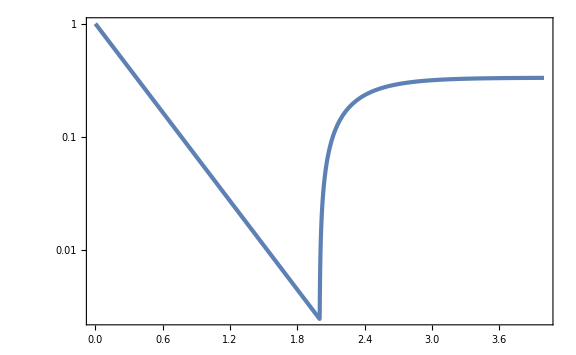

```mathematica
LogPlot[{dotx[t]}/.{H->1,dotxL->1,tL->0,tc->2,F0->-1},{t,0,4}]
```

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]
```

-(dotxc (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

```mathematica
xSR'[tc]
```

dotxc

```mathematica
xSR'[t]
```

dotxc ⅇ^(3 H (-t+tc))-(F0 (3 H-3 ⅇ^(3 H (-t+tc)) H))/(9 H^2)

```mathematica
xSR''[t]//Simplify
```

-ⅇ^(3 H (-t+tc)) (F0+3 dotxc H)

```mathematica
ZcIndet[t_]=Integrate[Exp[-3H (t-tc)]/xSR'[t]^2,t]
```

-(3 H)/(F0 ((-1+ⅇ^(3 H (t-tc))) F0-3 dotxc H))

```mathematica
Limit[ZcIndet[t],{t->∞},Assumptions->{H>0}]
```

0

```mathematica
Zc=-ZcIndet[tc]//Simplify
```

-1/(dotxc F0)

#### quadratic slope

```mathematica
xSR[t_]=Simplify[Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]
```

(dotxc (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))))/(Cm-Cp)+xc

```mathematica
xSR'[tc]
```

dotxc

```mathematica
xSR'[t]
```

(dotxc (Cm ⅇ^(Cm (t-tc))-Cp ⅇ^(Cp (t-tc))))/(Cm-Cp)

```mathematica
xSR''[t]
```

(dotxc (Cm^2 ⅇ^(Cm (t-tc))-Cp^2 ⅇ^(Cp (t-tc))))/(Cm-Cp)

```mathematica
Simplify[Normal[Series[(-3H+√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

m^2/(3 H)

```mathematica
Simplify[Normal[Series[(-3H-√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

-3 H-m^2/(3 H)

```mathematica
ZcIndet[t_]=Integrate[Exp[-3H (t-tc)]/xSR'[t]^2/.{Cp->m^2/(3H),Cm->-3H-m^2/(3H)},t]
```

-(3 H (9 H^2+2 m^2))/(dotxc^2 m^2 (9 H^2+(1+ⅇ^(((9 H^2+2 m^2) (t-tc))/(3 H))) m^2))

```mathematica
Limit[ZcIndet[t],{t->∞},Assumptions->{H>0,m>0}]
```

0

```mathematica
Zc=-ZcIndet[tc]//Simplify
```

(3 H)/(dotxc^2 m^2)